```mathematica
repeats=1;
conc=Table[{0,1,2.5,5,10,50,25,100},{i,1,repeats}];
```

```mathematica
proteinDilution=10; (*protein dilution factor before addition to 100μl well*)
proteinConc=4.56/proteinDilution; (*mg·ml^-1 from bradford*)
lysateDilutionInWell=100/20; (*20μl in 100μl assay*)
pathLength=0.26; (*10μl well volume*)
NADHExt=6.22 (*mM^-1 cm^-1*);
```

```mathematica
(*Quiet[Table[rangeCheck[i],{i,Length[dataPlots]}]]*)
```

```mathematica
rangeFolder="linearRanges";
```

|

{{0,5.27},{0,3.88},{0,4.06},{0,4.25},{0,5.21},{0,4.69},{1.47,7.56},{0,4.73}}

```mathematica
rates=Table[D[fits[[i]][x],x],{i,1,Length[fits]}]*(lysateDilutionInWell*proteinDilution/(NADHExt*pathLength*proteinConc))
```

{0.702068,0.743754,0.701626,0.694312,0.635843,0.532938,0.646626,0.438421}

```mathematica
(*Export[FileNameJoin[{dir,folder,rangeFolder,rangeFileName}],ranges]*)
```

|

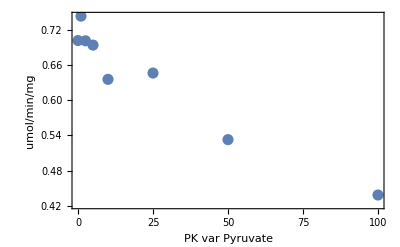

```mathematica
Pane[
,
Full,Alignment->Center]
```

```mathematica
headings={{"mM","V (umol/min/mg)"}};
```

PK var Pyruvate | 
mM | V (umol/min/mg)
0 | 0.702068
1 | 0.743754
2.5 | 0.701626
5 | 0.694312
10 | 0.635843
25 | 0.646626
50 | 0.532938
100 | 0.438421

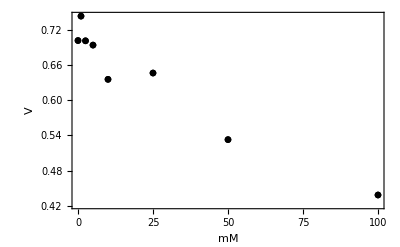

```mathematica
dataForExport=Join[headings,SortBy[rateData,First]];
```

### Data formatting:

```mathematica
allDataHeadings={{"PEP","ADP","Pyr","ATP","F16BP","V(umol/min/mg)"}};
```

#### vary PEP

```mathematica
(*dataFormatted={#[[1]],0.5,0,0,1,#[[2]]}&/@SortBy[rateData,First]*)
```

#### vary ADP:

```mathematica
(*dataFormatted={2.5,#[[1]],0,0,1,#[[2]]}&/@SortBy[rateData,First]*)
```

#### vary Pyr:

```mathematica
(*dataFormatted={1,0.5,#[[1]],0,0,#[[2]]}&/@rateData*)
```

#### vary ATP:

```mathematica
(*dataFormatted={2.5,5,#[[1]],0,0,#[[2]]}&/@rateData*)
```

#### vary F16BP:

```mathematica
(*dataFormatted={2.5,5,0,#[[1]],#[[2]]}&/@rateData*)
```

#### For Exporting

```mathematica
rateFolder = "outputRates";
rateFileName = StringDelete[fileName,{".xlsx"," "}]<>".csv";
(*Export[FileNameJoin[{dir,folder,rateFolder,rateFileName}],Join[allDataHeadings,dataFormatted]];*)
```